```mathematica
(* pie chart for university of kentucky *)
(* Sevahn Vorperian, Quake Lab *)
```

```mathematica
(* copying everything over here that is working because other notebook is a mess *)
```

```mathematica
fractions = Import["/Users/kayaneh/Documents/deconvolution/revision1/08012021_perComp_noEye_sigmat_18/adnci_v18_rmseAll_11282021/UniversityofKentucky_sigMat18_avgCoefs_plasma_1129021.csv"];
```

```mathematica
fractions
```

{{,University of Kentucky},{platelet,0.466946},{erythrocyte/erythroid progenitor,0.228323},{monocyte,0.0503676},{b cell,0.0263584},{neutrophil,0.0261024},{nk cell,0.0233015},{endothelial cell,0.0211276},{intestinal tuft cell,0.0146588},{adventitial cell,0.0103046},{t cell,0.00948647},{basophil,0.00901739},{salivary/bronchial secretory cell,0.00894578},{mature conventional dendritic cell,0.00878652},{basal cell,0.00835934},{thymocyte,0.00804427},{intestinal enterocyte,0.00654099},{intrahepatic cholangiocyte,0.00601431},{ionocyte/luminal epithelial cell of mammary gland,0.00595011},{respiratory ciliated cell,0.00592761},{cell of skeletal muscle,0.00573167},{schwann cell,0.00515091},{pericyte cell,0.00512562},{pancreatic alpha/beta cell,0.00498023},{salivary gland cell,0.0043925},{pancreatic stellate cell,0.00433692},{secretory cell,0.003529},{prostate epithelia,0.00300245},{hematopoietic stem cell,0.00186221},{mast cell,0.00183469},{intestinal secretory cell,0.0018214},{basal cell of prostate epithelium,0.00178241},{myeloid progenitor,0.00173809},{kidney epithelial cell,0.00147899},{type ii pneumocyte,0.0010577},{medullary thymic epithelial cell,0.00104338},{macrophage,0.000841621},{plasmablast,0.000806135},{club cell/type i pneumocyte,0.000748847},{respiratory secretory cell,0.00065163},{pancreatic ductal cell,0.000628531},{pancreatic pp cell,0.000507147},{pancreatic acinar cell,0.000490418},{mesothelial cell,0.000369357},{tendon cell,0.000331348},{stromal cell,0.00027416},{gland cell,0.000236732},{duodenum glandular cell,0.000226709},{goblet cell,0.000167011},{innate lymphoid cell,0.000121461},{luminal cell of prostate epithelium,0.0000814487},{plasma cell,0.0000726523},{keratinocyte,0.0000139418}}

```mathematica
roundPower = 0.1;
percentThresh = 1; (* percentage cutoff for stacked bar chart vs main pie *)
scalePercents = 100; (* scale all percentages by 100 *)
superSmallThresh = 0.1; (* percentage cutoff for cell types with small fractional contirbutions *)
sampleCenter = "University of Kentucky";
```

```mathematica
fractions;
```

```mathematica
fractions = fractions[[2;;]]; (* eliminate the center name *)
```

```mathematica
(* cellTypes = fractions[[1]][[2;;]] *)
cellTypes = fractions[[;;,1]];
```

```mathematica
(* fractions =fractions[[2;;,2;;]][[1]] *)
fractions = fractions[[;;,2]]
```

{0.466946,0.228323,0.0503676,0.0263584,0.0261024,0.0233015,0.0211276,0.0146588,0.0103046,0.00948647,0.00901739,0.00894578,0.00878652,0.00835934,0.00804427,0.00654099,0.00601431,0.00595011,0.00592761,0.00573167,0.00515091,0.00512562,0.00498023,0.0043925,0.00433692,0.003529,0.00300245,0.00186221,0.00183469,0.0018214,0.00178241,0.00173809,0.00147899,0.0010577,0.00104338,0.000841621,0.000806135,0.000748847,0.00065163,0.000628531,0.000507147,0.000490418,0.000369357,0.000331348,0.00027416,0.000236732,0.000226709,0.000167011,0.000121461,0.0000814487,0.0000726523,0.0000139418}

```mathematica
Length[fractions]
```

52

```mathematica
Length[cellTypes]
```

52

```mathematica
contribs = fractions  (* excluded sample name and r, p-value, RMSE *)
```

{0.466946,0.228323,0.0503676,0.0263584,0.0261024,0.0233015,0.0211276,0.0146588,0.0103046,0.00948647,0.00901739,0.00894578,0.00878652,0.00835934,0.00804427,0.00654099,0.00601431,0.00595011,0.00592761,0.00573167,0.00515091,0.00512562,0.00498023,0.0043925,0.00433692,0.003529,0.00300245,0.00186221,0.00183469,0.0018214,0.00178241,0.00173809,0.00147899,0.0010577,0.00104338,0.000841621,0.000806135,0.000748847,0.00065163,0.000628531,0.000507147,0.000490418,0.000369357,0.000331348,0.00027416,0.000236732,0.000226709,0.000167011,0.000121461,0.0000814487,0.0000726523,0.0000139418}

```mathematica
Length[fractions]
```

52

```mathematica
Length[cellTypes]
```

52

```mathematica
(* first get the zero index *)
```

```mathematica
zeroIndex = Position[contribs, val_/;val ≤ 0]
```

{}

```mathematica
(* drop it from the contributions and drop the corresponding labels *)
```

```mathematica
nonZeroVals = Delete[contribs, zeroIndex];
```

```mathematica
nonZeroVals = nonZeroVals * scalePercents
```

{46.6946,22.8323,5.03676,2.63584,2.61024,2.33015,2.11276,1.46588,1.03046,0.948647,0.901739,0.894578,0.878652,0.835934,0.804427,0.654099,0.601431,0.595011,0.592761,0.573167,0.515091,0.512562,0.498023,0.43925,0.433692,0.3529,0.300245,0.186221,0.183469,0.18214,0.178241,0.173809,0.147899,0.10577,0.104338,0.0841621,0.0806135,0.0748847,0.065163,0.0628531,0.0507147,0.0490418,0.0369357,0.0331348,0.027416,0.0236732,0.0226709,0.0167011,0.0121461,0.00814487,0.00726523,0.00139418}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
nonZeroCells = Delete[cellTypes, zeroIndex];
```

```mathematica
Length[nonZeroCells]
```

52

```mathematica
nonZeroCells
```

{platelet,erythrocyte/erythroid progenitor,monocyte,b cell,neutrophil,nk cell,endothelial cell,intestinal tuft cell,adventitial cell,t cell,basophil,salivary/bronchial secretory cell,mature conventional dendritic cell,basal cell,thymocyte,intestinal enterocyte,intrahepatic cholangiocyte,ionocyte/luminal epithelial cell of mammary gland,respiratory ciliated cell,cell of skeletal muscle,schwann cell,pericyte cell,pancreatic alpha/beta cell,salivary gland cell,pancreatic stellate cell,secretory cell,prostate epithelia,hematopoietic stem cell,mast cell,intestinal secretory cell,basal cell of prostate epithelium,myeloid progenitor,kidney epithelial cell,type ii pneumocyte,medullary thymic epithelial cell,macrophage,plasmablast,club cell/type i pneumocyte,respiratory secretory cell,pancreatic ductal cell,pancreatic pp cell,pancreatic acinar cell,mesothelial cell,tendon cell,stromal cell,gland cell,duodenum glandular cell,goblet cell,innate lymphoid cell,luminal cell of prostate epithelium,plasma cell,keratinocyte}

```mathematica
nonZeroVals
```

{46.6946,22.8323,5.03676,2.63584,2.61024,2.33015,2.11276,1.46588,1.03046,0.948647,0.901739,0.894578,0.878652,0.835934,0.804427,0.654099,0.601431,0.595011,0.592761,0.573167,0.515091,0.512562,0.498023,0.43925,0.433692,0.3529,0.300245,0.186221,0.183469,0.18214,0.178241,0.173809,0.147899,0.10577,0.104338,0.0841621,0.0806135,0.0748847,0.065163,0.0628531,0.0507147,0.0490418,0.0369357,0.0331348,0.027416,0.0236732,0.0226709,0.0167011,0.0121461,0.00814487,0.00726523,0.00139418}

```mathematica
(* nonZeroVals = nonZeroVals/Total[nonZeroVals] (* normalize to 1 *) did this normalization in python *)
```

```mathematica
nonZeroVals = Round[#, roundPower] &/@nonZeroVals (* round to 3 digits *)
```

{46.7,22.8,5.,2.6,2.6,2.3,2.1,1.5,1.,0.9,0.9,0.9,0.9,0.8,0.8,0.7,0.6,0.6,0.6,0.6,0.5,0.5,0.5,0.4,0.4,0.4,0.3,0.2,0.2,0.2,0.2,0.2,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Total[nonZeroVals]
```

99.8

```mathematica
(* get index cell types that are less than one percent together for the bar chart *)
```

```mathematica
lt1Percent = Position[nonZeroVals, val_/;val  < percentThresh]
```

{{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52}}

```mathematica
(* now pull the cell types and their associated values and put in reverse order so it goes from smallest to largest *)
```

```mathematica
smallContribVals = Reverse[Part[nonZeroVals, # ]&/@ lt1Percent]
smallContribCells = Reverse[Part[nonZeroCells, #] &/@ lt1Percent];
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.1},{0.1},{0.1},{0.1},{0.1},{0.1},{0.1},{0.1},{0.1},{0.2},{0.2},{0.2},{0.2},{0.2},{0.3},{0.4},{0.4},{0.4},{0.5},{0.5},{0.5},{0.6},{0.6},{0.6},{0.6},{0.7},{0.8},{0.8},{0.9},{0.9},{0.9},{0.9}}

```mathematica
(* get the indices where the elements are ≤ 0.1% or 0.001 *)
```

```mathematica
ltPt1Percent = Position[Flatten[smallContribVals], val_/;val  ≤ superSmallThresh]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20}}

```mathematica
(* get the sum of the values and the respective cell ≤ 0.1 % *)
fracsLTPt1 = Part[smallContribVals, # ] &/@ ltPt1Percent
cellsLTPt1 = Part[smallContribCells, #] &/@ ltPt1Percent
```

{{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}}}

{{{keratinocyte}},{{plasma cell}},{{luminal cell of prostate epithelium}},{{innate lymphoid cell}},{{goblet cell}},{{duodenum glandular cell}},{{gland cell}},{{stromal cell}},{{tendon cell}},{{mesothelial cell}},{{pancreatic acinar cell}},{{pancreatic pp cell}},{{pancreatic ductal cell}},{{respiratory secretory cell}},{{club cell/type i pneumocyte}},{{plasmablast}},{{macrophage}},{{medullary thymic epithelial cell}},{{type ii pneumocyte}},{{kidney epithelial cell}}}

```mathematica
totalSuperSmall = Total[Flatten[fracsLTPt1]]
```

0.9

```mathematica
(* now drop those small guys *)
```

```mathematica
goodSmallVals = Delete[smallContribVals, ltPt1Percent];
goodSmallCells = Delete[smallContribCells, ltPt1Percent];
```

```mathematica
goodSmallCells
```

{{myeloid progenitor},{basal cell of prostate epithelium},{intestinal secretory cell},{mast cell},{hematopoietic stem cell},{prostate epithelia},{secretory cell},{pancreatic stellate cell},{salivary gland cell},{pancreatic alpha/beta cell},{pericyte cell},{schwann cell},{cell of skeletal muscle},{respiratory ciliated cell},{ionocyte/luminal epithelial cell of mammary gland},{intrahepatic cholangiocyte},{intestinal enterocyte},{thymocyte},{basal cell},{mature conventional dendritic cell},{salivary/bronchial secretory cell},{basophil},{t cell}}

```mathematica
(* add the sum of the remaining cells *)
goodSmallVals = AppendTo[goodSmallVals, {totalSuperSmall}]
goodSmallCells = AppendTo[goodSmallCells, {"Very Small Contributors"}]
```

{{0.2},{0.2},{0.2},{0.2},{0.2},{0.3},{0.4},{0.4},{0.4},{0.5},{0.5},{0.5},{0.6},{0.6},{0.6},{0.6},{0.7},{0.8},{0.8},{0.9},{0.9},{0.9},{0.9},{0.9}}

{{myeloid progenitor},{basal cell of prostate epithelium},{intestinal secretory cell},{mast cell},{hematopoietic stem cell},{prostate epithelia},{secretory cell},{pancreatic stellate cell},{salivary gland cell},{pancreatic alpha/beta cell},{pericyte cell},{schwann cell},{cell of skeletal muscle},{respiratory ciliated cell},{ionocyte/luminal epithelial cell of mammary gland},{intrahepatic cholangiocyte},{intestinal enterocyte},{thymocyte},{basal cell},{mature conventional dendritic cell},{salivary/bronchial secretory cell},{basophil},{t cell},{Very Small Contributors}}

```mathematica
(* now sort this finalized "small cell" list *)
```

```mathematica
finalOrder = Reverse[Ordering[goodSmallVals]]
```

{24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
goodSmallVals = Flatten[Part[goodSmallVals , #] &/@ finalOrder]
```

{0.9,0.9,0.9,0.9,0.9,0.8,0.8,0.7,0.6,0.6,0.6,0.6,0.5,0.5,0.5,0.4,0.4,0.4,0.3,0.2,0.2,0.2,0.2,0.2}

```mathematica
goodSmallCells = Flatten[Part[goodSmallCells, #] &/@ finalOrder]
```

{Very Small Contributors,t cell,basophil,salivary/bronchial secretory cell,mature conventional dendritic cell,basal cell,thymocyte,intestinal enterocyte,intrahepatic cholangiocyte,ionocyte/luminal epithelial cell of mammary gland,respiratory ciliated cell,cell of skeletal muscle,schwann cell,pericyte cell,pancreatic alpha/beta cell,salivary gland cell,pancreatic stellate cell,secretory cell,prostate epithelia,hematopoietic stem cell,mast cell,intestinal secretory cell,basal cell of prostate epithelium,myeloid progenitor}

```mathematica
(* now make the bar chart *)
```

```mathematica
shortlist =List[Flatten[Table[Callout[goodSmallVals[[#]], goodSmallCells[[#]],After,Appearance->"Leader",LeaderSize->{15,Automatic,2}],1] &/@Range[Length[goodSmallCells]]]];
```

```mathematica
shortlist
```

{{Callout[0.9,Very Small Contributors,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,t cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,basophil,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,salivary/bronchial secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,mature conventional dendritic cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.8,basal cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.8,thymocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,intestinal enterocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,intrahepatic cholangiocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,ionocyte/luminal epithelial cell of mammary gland,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,respiratory ciliated cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,cell of skeletal muscle,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,schwann cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,pericyte cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,pancreatic alpha/beta cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,salivary gland cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,pancreatic stellate cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.3,prostate epithelia,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,hematopoietic stem cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,mast cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,intestinal secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,basal cell of prostate epithelium,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,myeloid progenitor,After,Appearance→Leader,LeaderSize→{15,Automatic,2}]}}

```mathematica
piePal = Map [RGBColor,{"#bee9e8","#62b6cb","#1b4965","#cae9ff","#5fa8d3", "#f26419", "#a4508b", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab", "#5bba6f", "#9ece9a", "#c8d5b9"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313]}

```mathematica
(* would use LabelingSize function but its not available before version 11.3 
https://reference.wolfram.com/language/ref/LabelingSize.html*)
```

```mathematica
barHexList = {"#0081a7","#06BEE1","#00afb9","#6d597a","#d62828","#f07167","#f77f00","#fcbf49","#eae2b7","#C2E7D9","#89b0ae", "#7EBDC2", "#C0E8F9", "#B56576", "#6D597A", "#355070","#457b9d","#6096ba","#555b6e","#414770", "#5B85AA","#355070","#b56576","#E56B6F","#EAAC8B","#f6ae2d","#FFBF81","#FFD9CE"}
```

{#0081a7,#06BEE1,#00afb9,#6d597a,#d62828,#f07167,#f77f00,#fcbf49,#eae2b7,#C2E7D9,#89b0ae,#7EBDC2,#C0E8F9,#B56576,#6D597A,#355070,#457b9d,#6096ba,#555b6e,#414770,#5B85AA,#355070,#b56576,#E56B6F,#EAAC8B,#f6ae2d,#FFBF81,#FFD9CE}

```mathematica
Tally[barHexList]
```

{{#0081a7,1},{#06BEE1,1},{#00afb9,1},{#6d597a,1},{#d62828,1},{#f07167,1},{#f77f00,1},{#fcbf49,1},{#eae2b7,1},{#C2E7D9,1},{#89b0ae,1},{#7EBDC2,1},{#C0E8F9,1},{#B56576,1},{#6D597A,1},{#355070,2},{#457b9d,1},{#6096ba,1},{#555b6e,1},{#414770,1},{#5B85AA,1},{#b56576,1},{#E56B6F,1},{#EAAC8B,1},{#f6ae2d,1},{#FFBF81,1},{#FFD9CE,1}}

```mathematica
Map[RGBColor, {"#355070"}]
```

{RGBColor[0.20784313725490197, 0.3137254901960784, 0.4392156862745098]}

```mathematica
barPal = Map[RGBColor, {"#0081a7","#06BEE1","#00afb9","#61A5C2","#168AAD","#6d597a","#d62828","#f07167","#f77f00","#fcbf49","#eae2b7","#C2E7D9","#89b0ae",
 "#A9D6E5","#7EBDC2",
  "#468FAF", "#2A6F97", "#5B85AA",
  (* "#276FBF", *)"#457b9d","#6096ba",
"#414770", "#6D597A", "#b56576",(*"#E56B6F",*)"#FFBF81","#FFD9CE"}]
```

{RGBColor[0., 0.5058823529411764, 0.6549019607843137],RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],RGBColor[0., 0.6862745098039216, 0.7254901960784313],RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],RGBColor[0.9686274509803922, 0.4980392156862745, 0.],RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.2549019607843137, 0.2784313725490196, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[1., 0.7490196078431373, 0.5058823529411764],RGBColor[1., 0.8509803921568627, 0.807843137254902]}

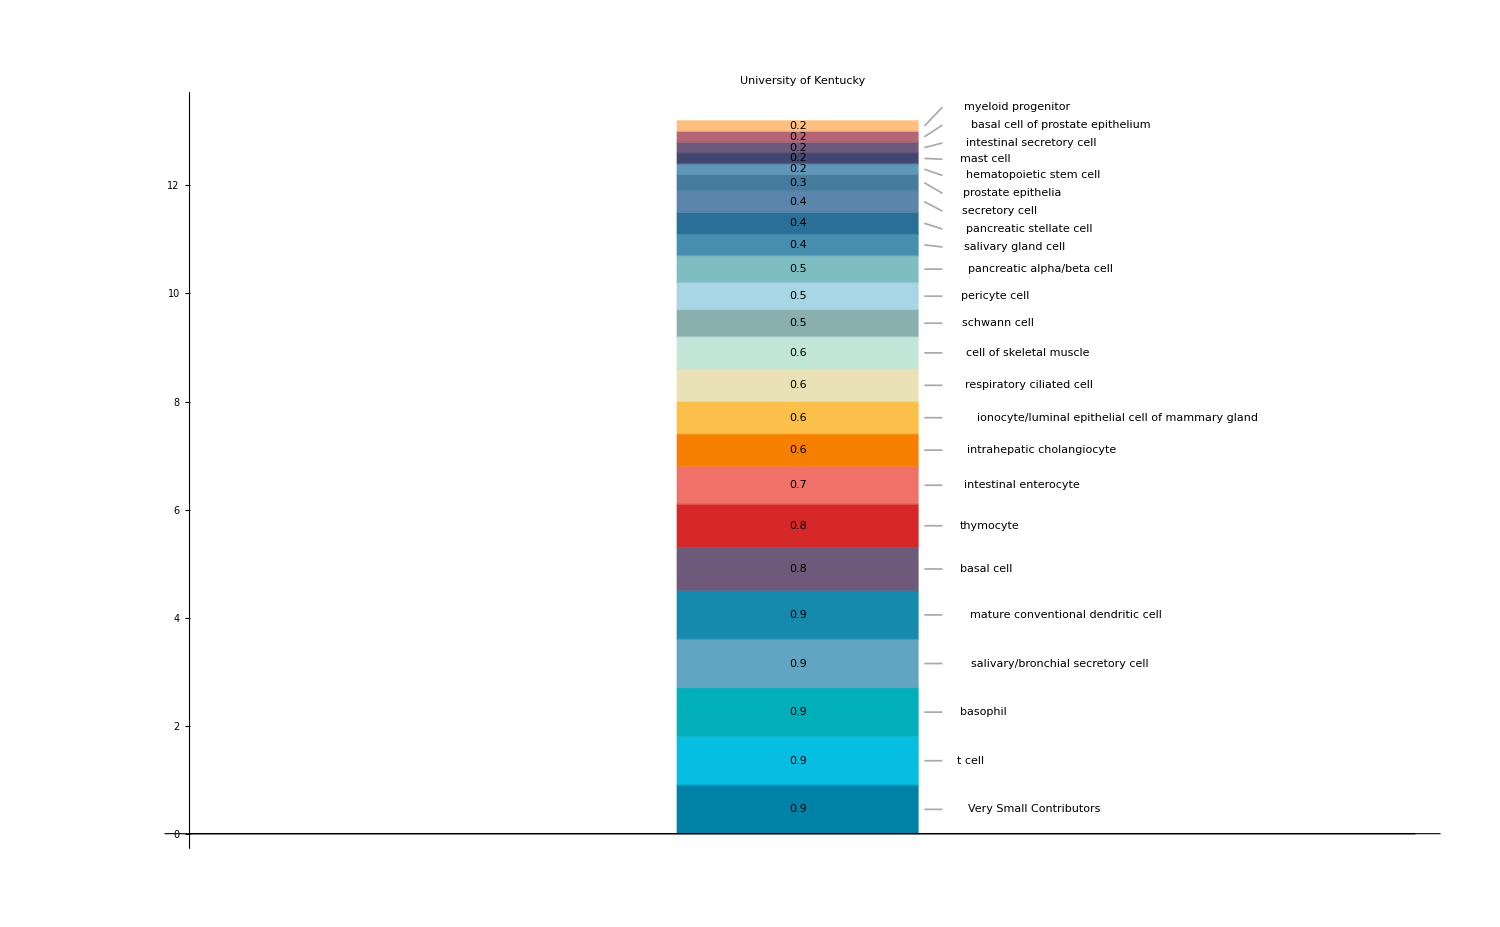

```mathematica
BarChart[shortlist,BarSpacing->2,ChartLayout->"Stacked",
ChartStyle-> barPal, ImageSize-> 1500, LabelingFunction ->( Placed[#1, Center]&), BaseStyle->{FontSize->15}, PlotLabel -> sampleCenter]
```

```mathematica
(* cool, now it's time to make the pie chart *)
```

```mathematica
gtPt1Percent = Position[Flatten[nonZeroVals], val_/;val  >=percentThresh ]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9}}

```mathematica
bigContribs = Part[nonZeroVals, #] &/@ gtPt1Percent
```

{{46.7},{22.8},{5.},{2.6},{2.6},{2.3},{2.1},{1.5},{1.}}

```mathematica
bigCells = Part[nonZeroCells, #] &/@ gtPt1Percent
```

{{platelet},{erythrocyte/erythroid progenitor},{monocyte},{b cell},{neutrophil},{nk cell},{endothelial cell},{intestinal tuft cell},{adventitial cell}}

```mathematica
bigTot = Total[Flatten[bigContribs]] ;
smallContribTot = Total[Flatten[goodSmallVals]];
bigTot + smallContribTot (* cool, so we sum to 1 between small and big contributions *)
```

99.8

```mathematica
(* add the sum of the small contributions *)
```

```mathematica
bigContribs= AppendTo[bigContribs, {smallContribTot}];
bigCells = AppendTo[bigCells, {"Small"}]
```

{{platelet},{erythrocyte/erythroid progenitor},{monocyte},{b cell},{neutrophil},{nk cell},{endothelial cell},{intestinal tuft cell},{adventitial cell},{Small}}

```mathematica
Total[Flatten[bigContribs]]
```

99.8

```mathematica
(* now it's time to sort it from big to small *)
```

```mathematica
finalOrderBig = Reverse[Ordering[bigContribs]];
bigContribs = Flatten[Part[bigContribs, #] &/@ finalOrderBig];
bigCells = Flatten[Part[bigCells, #] &/@ finalOrderBig];
```

```mathematica
(* make the labels for the pie chart *)
```

```mathematica
bigContribs
```

{46.7,22.8,13.2,5.,2.6,2.6,2.3,2.1,1.5,1.}

```mathematica
test = Callout[bigContribs[[#]], bigCells[[#]],  Appearance -> "Leader"]&/@ Range[Length[bigCells]]
```

{Callout[46.7,platelet,Appearance→Leader],Callout[22.8,erythrocyte/erythroid progenitor,Appearance→Leader],Callout[13.2,Small,Appearance→Leader],Callout[5.,monocyte,Appearance→Leader],Callout[2.6,neutrophil,Appearance→Leader],Callout[2.6,b cell,Appearance→Leader],Callout[2.3,nk cell,Appearance→Leader],Callout[2.1,endothelial cell,Appearance→Leader],Callout[1.5,intestinal tuft cell,Appearance→Leader],Callout[1.,adventitial cell,Appearance→Leader]}

```mathematica
"#84a98c"
```

#84a98c

```mathematica
Map[RGBColor,{ "#457b9d","#6096ba","#555b6e", "#355070","#eaac8b","#b56576","#f6ae2d"}]
```

{RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.3333333333333333, 0.3568627450980392, 0.43137254901960786],RGBColor[0.20784313725490197, 0.3137254901960784, 0.4392156862745098],RGBColor[0.9176470588235294, 0.6745098039215687, 0.5450980392156862],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413]}

```mathematica
piePal = Map [RGBColor,{"#bee9e8" ,"#62b6cb","#1b4965","#cae9ff","#5fa8d3",
"#6d597a",
 "#a4508b", "#BC412B","#f26419","#f8c7cc", "#f7567c",
"#e56b6f","#f6ae2d","#68b0ab",  "#84a98c", "#5bba6f", "#9ece9a", "#c8d5b9","#89b0ae" }]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.7372549019607844, 0.2549019607843137, 0.16862745098039217],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.9725490196078431, 0.7803921568627451, 0.8],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.8980392156862745, 0.4196078431372549, 0.43529411764705883],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.5176470588235295, 0.6627450980392157, 0.5490196078431373],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706]}

```mathematica
(* piePal = Map [RGBColor,{"#bee9e8" ,"#62b6cb","#1b4965","#cae9ff","#5fa8d3",  "#a4508b", "#BC412B","#f26419","#f8c7cc", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab","#84a98c", "#5bba6f", "#9ece9a", "#c8d5b9", "#6d597a","#b56576","#e56b6f","#eaac8b","#89b0ae",  "#457b9d","#6096ba","#555b6e", "#355070"}] *)
```

```mathematica
{ro, rc} = PieChart[test, ChartStyle->piePal, SectorOrigin->{ 5 Pi / 10,"Counterclockwise"},BaseStyle->{FontSize->15},  ImageSize-> 1500,ImagePadding->{{240,60},{0,0}},LabelingFunction ->#, PlotLabel->sampleCenter] &/@{"RadialOuter", "RadialCenter"}
Row[{ro,rc}];
```

{-Graphics-,-Graphics-}

```mathematica
{radiuso,radiusc}=First@Cases[#,Text[_,p_,___]:>Norm[p],All]&/@{ro,rc}
```

{0.9,0.666667}

```mathematica
rm=Show[rc/.Text[t_,p_,x___]:>Text[t,Mean[{radiuso,radiusc}] Normalize[p],x]]
```

-Graphics-

```mathematica
PieChart[test, ChartStyle->piePal, SectorOrigin->{  13.5Pi / 10,"Clockwise"},BaseStyle->{FontSize->15},  ImageSize-> 1500,ImagePadding->{{240,60},{0,0}},LabelingFunction ->"RadialCenter", PlotLabel->sampleCenter]
```

-Graphics-

```mathematica
(* could try adding percents to the fractions but i wont *)
```

```mathematica
stringPercents = TextString[bigContribs[[#]]]<>"%" &/@ Range[Length[bigContribs]]
```

{46.7%,22.8%,13.2%,5.0%,2.6%,2.6%,2.3%,2.1%,1.5%,1.0%}